Here, I consider the result of mutant invasion in a cycling population with the purpose of generating a pairwise invasibility plot. This occurs when average specialist payoff exceeds average generalist payoff. First I’ll consider the outcome of  an invading alpha mutant along a cycle’s period. Below is our system of equations denoting the frequency of each strategist.

```mathematica
(*x -> the proportion of a host's resource that is shared*)
(*α -> the matched exchange rate*)
(*(1-α^(1/c))^c -> the mismatched exchange rate, f(α)*)
(*αg -> the generalist exchange rate*)
payoffs={x*(α−x),
x*((1-α^(1/c))^c−x),
x*(αg−x),
x*(1−α),
x*(1−(1-α^(1/c))^c),
x*(1−αg)};(*Payoffs for hosts (1 through 3)and symbionts (4 through 6)*)
```

```mathematica
{pi1,pi1',pig,ψ1,ψ1',ψg1}=payoffs;(*Resident host payoffs: pi1 = match, pi1' = msimatch, and pig = generalist. Payoffs for a symbiont interacting with host 1: ψ1 = match,ψ1' = mismatch,ψg1 = generalist)*)
{pi1m,pi1m',pig1m,ψ1m,ψ1m',ψg1m}=payoffs/.{α-> αm};
(*Payoffs received when interacting with a mutant host *)
```

Next we find the average payoffs of each strategist:

```mathematica
S1 = v1*ψ1+v2*ψ1'+m1*ψ1m+(1−v−p-m1)*ψg1 ;(*Symbiont 1 *)
S2 =  v1*ψ1'+v2*ψ1+m1*ψ1m'+(1−v−p-m1)*ψg1; (*Symbiont 2 *)
H1=u*pi1+(1-u)*pi1';(*Host 1 *)
H2 = u*pi1'+(1−u)*pi1;(*Host 2 *)
HM1=u*pi1m+(1-u)*pi1m';(*Host 1 mutant*)
HG = pig;(*Generalist Host*)
Hbar = v1*H1+v2*H2+m1*HM1+(1-v1-v2-m1)*HG;(*Payoff received by a host on average*)
```

Finally, we’ll find expressions for the frequency of each strategist:

```mathematica
S = u(1-u)(S1-S2);(*Symbiont 1*)
V1=v1(H1-Hbar);(*Host 1*)
V2=v2(H2-Hbar);(*Host 2*)
M1=m1(HM1-Hbar);(*Host 1 Mutant*)
```

Now we can put these equations together in a system:

```mathematica
replicators2={S,V1,V2,M1}/.{v1-> v1[t],v2-> v2[t],m1-> m1[t], u-> u[t]};
```

Finally, we’ll find expressions for the frequency of each strategist:

```mathematica
System[α_,αm_, αg_,c_,x_,u0_,v10_,v20_,m10_]:={u'[t]==(1-u[t]) u[t] (x (1-αm) m1[t]-x (1-(1-αm^(1/c))^c) m1[t]+x (1-α) v1[t]-x (1-(1-α^(1/c))^c) v1[t]-x (1-α) v2[t]+x (1-(1-α^(1/c))^c) v2[t]),v1'[t]==v1[t] (x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]-m1[t] (x (-x+(1-αm^(1/c))^c) (1-u[t])+x (-x+αm) u[t])-(x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]) v1[t]-x (-x+αg) (1-m1[t]-v1[t]-v2[t])-(x (-x+α) (1-u[t])+x (-x+(1-α^(1/c))^c) u[t]) v2[t]),v2'[t]==v2[t] (x (-x+α) (1-u[t])+x (-x+(1-α^(1/c))^c) u[t]-m1[t] (x (-x+(1-αm^(1/c))^c) (1-u[t])+x (-x+αm) u[t])-(x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]) v1[t]-x (-x+αg) (1-m1[t]-v1[t]-v2[t])-(x (-x+α) (1-u[t])+x (-x+(1-α^(1/c))^c) u[t]) v2[t]),m1'[t]==m1[t] (x (-x+(1-αm^(1/c))^c) (1-u[t])+x (-x+αm) u[t]-m1[t] (x (-x+(1-αm^(1/c))^c) (1-u[t])+x (-x+αm) u[t])-(x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]) v1[t]-x (-x+αg) (1-m1[t]-v1[t]-v2[t])-(x (-x+α) (1-u[t])+x (-x+(1-α^(1/c))^c) u[t]) v2[t]),u[0]==u0,v1[0]==-m10+v10,m1[0]==m10,v2[0]==v20,(*Restrict frequencies of strategists to [0,1]: *)WhenEvent [EvenQ[0]&&m1[t]<0, m1[t]-> 0,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&v2[t]<0, v2[t]-> 0,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&u[t]<0, u[t]-> 0,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&v1[t]<0, v1[t]-> 0,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&m1[t]>1, m1[t]-> 1,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&v2[t]>1, v2[t]-> 1,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&u[t]>1, u[t]-> 1,"LocationMethod"->"LinearInterpolation"],WhenEvent [EvenQ[0]&&v1[t]>1, v1[t]-> 1,"LocationMethod"->"LinearInterpolation"]}(*Here, we format this system appropriately for our simulations note that we begin from initial conditions for u, Subscript[v, 1], v2, v1m and v2m given by u0, v10, v20, v1m0 and v2m0 respectively*)
```

Our goal is to determine when mutants will be able to successfully beat out residents on average across a resident’s cycle. First we will consider what vaules of extraction it will be reasonable to test in our simulations for a concave down tradeoff function. We will do so by plotting our tradeoff function, and the generalist and specialist payoffs as a function of

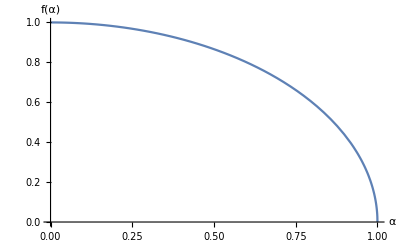

```mathematica
Plot[((1-α^(1/c))^c)/.{ c-> 1/2}, {α,0,1}, PlotLegends-> Automatic, AxesLabel->{"α","f(α)"}]
```

And the relationship between specialist average payoff and generalist payoff:

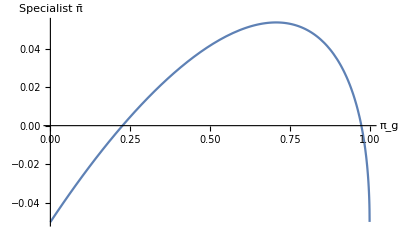

```mathematica
difference2=((pi1+pi1')/2)-pig/.{x-> 0.5,c-> 1/2, αg-> 0.6};
Plot[difference2, {α, 0,1},AxesLabel->{"π_g","Specialist π̄"}]
```

```mathematica
Solve[difference2==0,α]
```

{{α→0.225834},{α→0.974166}}

Given these parameters we’ll need to restrict our values of alpha to this domain.

Now let’s determine the cycle periods associated with this domain:

```mathematica
CCPeriods=ParallelTable[{αr,
(*Establish a Resident Population:*)
sol=NDSolve[System[αr,0,0.6,1/2,0.6,0.25,0.28,0.24,0],{u,v1,v2,m1},{t,0,30000},Method->{"StiffnessSwitching"},MaxSteps->10^6];
{uans,v1ans,v2ans,m1ans}= {u[t],v1[t],v2[t],m1[t]}  /.Flatten[sol];
data=Table[{t-8000,v1ans},{t,8000,9100,0.1}];
(*Fit a sinusoidal function to the cycle of the resident host and determine its period: *)
Parameters =FindFit[data,{a*Sin[b*(t+c)]+d},{a,b,c,d},t, Method->"NMinimize"];
T1=Abs[(2*π/b)/.Parameters[[2]]];
T1}
,{αr,0.23,0.97,0.01}];
```

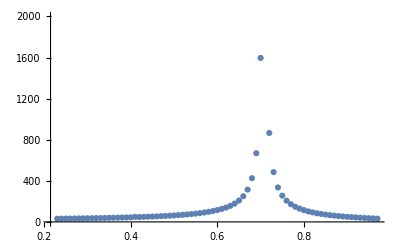

```mathematica
ListPlot[CCPeriods, PlotRange-> {0,2000}]
```

Because this plot of discontinuities looks good to go, we know that our range is reasonable.

```mathematica
(*here we define a fuction to find the average frequency of a given strategist.*)
FindAverage[fun_,a_,b_]:=(1/(b-a))*NIntegrate[fun,{t,a,b},WorkingPrecision->8, AccuracyGoal-> 8];
```

```mathematica
(*Now for the concave down tradeoff function: *)
PIPCC=ParallelTable[{αr,αm,
(*Establish a Resident Population with arbitrary initial frequencies:*)
sol=NDSolve[System[αr,0,0.6,1/2,0.5,0.25,0.28,0.24,0],{u,v1,v2,m1},{t,0,30000},Method->{"StiffnessSwitching"},MaxSteps->10^6];
{uans,v1ans,v2ans,m1ans}= {u[t],v1[t],v2[t],m1[t]}  /.Flatten[sol];
data=Table[{t-8000,v1ans},{t,8000,9100,0.1}];
(*Fit NDSolve output to sin function and find the period for the resident population:*)
Parameters =FindFit[data,{a*Sin[b*(t+c)]+d},{a,b,c,d},t, Method->"NMinimize"];
T1=Abs[(2*π/b)/.Parameters[[2]]];
T1,
(*Introduce mutant invaders at each 0.1*T1 of the cycle:*)
SampleInvasion=Table[{st,
{uf, v1f,v2f,m1f}={u[st],v1[st],v2[st],m1[st]}/.Flatten[sol];                   sol2=NDSolve[System[αr,αm,0.6,1/2,0.5,uf,v1f,v2f,0.05],{u,v1,v2,m1},{t,0,7*T1},Method->{"StiffnessSwitching"},MaxSteps->10^6];
{uans,v1ans,v2ans,m1ans}= {u[t],v1[t],v2[t],m1[t]}  /.Flatten[sol2];

(*Average mutant frequency several Periods after they invade:*)
m1avg=FindAverage[m1ans,4*T1,7*T1];

If[m1avg>0.05,1,0](*If mutant average frequency has increased from its initial low frequency, we deem this a successful invasion*)}
,
{st,8000,8000+T1,0.01*T1}];

(*Determine if on average the mutants successfully Invade:*)
FlattenedSample=Flatten[SampleInvasion];
AvgResult=Mean[Take[FlattenedSample,{2,-1,2}]];
(*This is the average frequency with which the mutant successfully invaded: *)
AvgResult,
(*Finally, this is a bindary definition of successful invasion: *)
If[AvgResult>0.5,1,0]},
{αr,0.23,0.97,0.01},{αm,0.23,0.97,0.01}];
```

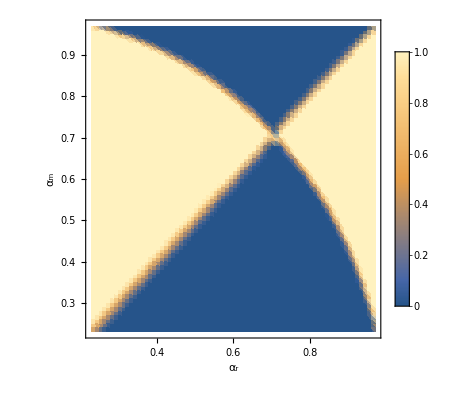

```mathematica
PIPCCF=Flatten[PIPCC,1];
PlotCC=PIPCCF[[All,{1,2,4}]];
ListDensityPlot[PlotCC,PlotLegends->Automatic,  FrameLabel->{"α_r","α_m"}]
```

```mathematica
Export["ConCaveInvasionFinal.csv",PIPCC];
```

Next, we’ll consider mutant invasion when the tradeoff is concave up (i.e. convex). First, we’ll consider what trait values to consider:

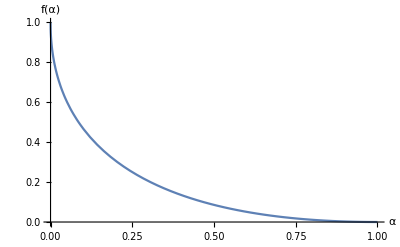

```mathematica
Plot[((1-α^(1/c))^c)/.{ c->2}, {α,0,1}, PlotLegends-> Automatic, AxesLabel->{"α","f(α)"}]
```

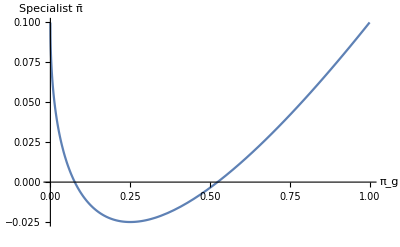

```mathematica
difference2=((pi1+pi1')/2)-pig/.{x-> 0.5,c-> 2, αg-> 0.3};
Plot[difference2, {α, 0,1},AxesLabel->{"π_g","Specialist π̄"}]
(**)
```

```mathematica
Solve[difference2==0,α]
```

{{α→0.0763932},{α→0.523607}}

So we’ll restrict α to be greater than 0.523. We won’t test the lower range of this domain because in this region hosts would simply be evolving to specialize on their mismatched symbiont, thus its dynamics are the same.

```mathematica
CVPeriods=ParallelTable[{αr,
(*Establish a Resident Population:*)
sol=NDSolve[System[αr,0,0.3,2,0.5,0.25,0.28,0.24,0],{u,v1,v2,m1},{t,0,30000},Method->{"StiffnessSwitching"},MaxSteps->10^6];
{uans,v1ans,v2ans,m1ans}= {u[t],v1[t],v2[t],m1[t]}  /.Flatten[sol];
data=Table[{t-8000,v1ans},{t,8000,9100,0.1}];
(*Fit a sinusoidal function to the cycle of the resident host and determine its period: *)
Parameters =FindFit[data,{a*Sin[b*(t+c)]+d},{a,b,c,d},t, Method->"NMinimize"];
T1=Abs[(2*π/b)/.Parameters[[2]]];
T1}
,{αr,0.55,0.99,0.01}];
```

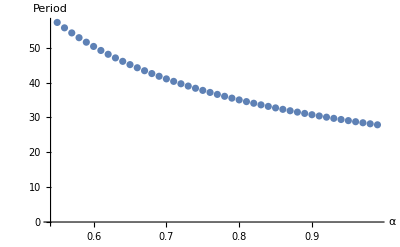

```mathematica
ListPlot[CVPeriods,AxesLabel->{"α","Period"}]
```

Because this plot of discontinuities looks good to go, we know that our range is reasonable.

```mathematica
(*Now for the concave down tradeoff function: *)
PIPCV=ParallelTable[{αr,αm,
(*Establish a Resident Population with arbitrary initial frequencies:*)
sol=NDSolve[System[αr,0,0.3,2,0.5,0.25,0.28,0.24,0],{u,v1,v2,m1},{t,0,30000},Method->{"StiffnessSwitching"},MaxSteps->10^6];
{uans,v1ans,v2ans,m1ans}= {u[t],v1[t],v2[t],m1[t]}  /.Flatten[sol];
data=Table[{t-8000,v1ans},{t,8000,9100,0.1}];
(*Fit NDSolve output to sin function and find the period for the resident population:*)
Parameters =FindFit[data,{a*Sin[b*(t+c)]+d},{a,b,c,d},t, Method->"NMinimize"];
T1=Abs[(2*π/b)/.Parameters[[2]]];
T1,
(*Introduce mutant invaders at each 0.1*T1 of the cycle:*)
SampleInvasion=Table[{st,
{uf, v1f,v2f,m1f}={u[st],v1[st],v2[st],m1[st]}/.Flatten[sol];                   sol2=NDSolve[System[αr,αm,0.3,2,0.5,uf,v1f,v2f,0.05],{u,v1,v2,m1},{t,0,7*T1},Method->{"StiffnessSwitching"},MaxSteps->10^6];
{uans,v1ans,v2ans,m1ans}= {u[t],v1[t],v2[t],m1[t]}  /.Flatten[sol2];

(*Average mutant frequency several Periods after they invade:*)
m1avg=FindAverage[m1ans,4*T1,7*T1];

If[m1avg>0.05,1,0](*If mutant average frequency has increased from its initial low frequency, we deem this a successful invasion*)}
,
{st,8000,8000+T1,0.01*T1}];

(*Determine if on average the mutants successfully Invade:*)
FlattenedSample=Flatten[SampleInvasion];
AvgResult=Mean[Take[FlattenedSample,{2,-1,2}]];
(*This is the average frequency with which the mutant successfully invaded: *)
AvgResult,
(*Finally, this is a bindary definition of successful invasion: *)
If[AvgResult>0.5,1,0]},
{αr,0.55,0.99,0.01},{αm,0.55,0.99,0.01}];
```

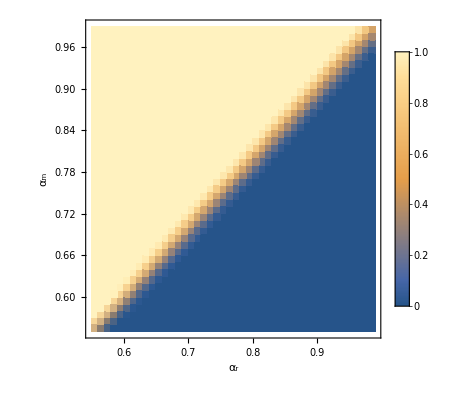

```mathematica
Export["ConvexInvasionFinal.csv",PIPCV];
PIPCVF=Flatten[PIPCV,1];
PlotCV=PIPCVF[[All,{1,2,4}]];
ListDensityPlot[PlotCV,PlotLegends->Automatic,  FrameLabel->{"α_r","α_m"}]
```

Finally, the linear tradeoff:

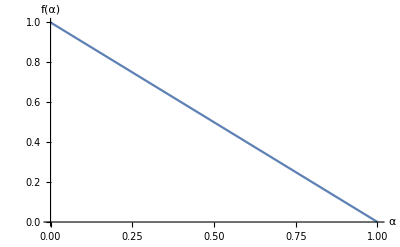

```mathematica
Plot[((1-α^(1/c))^c)/.{ c-> 1}, {α,0,1}, PlotLegends-> Automatic, AxesLabel->{"α","f(α)"}]
```

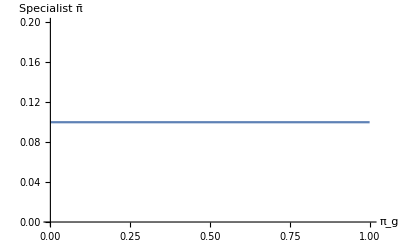

```mathematica
difference2=((pi1+pi1')/2)-pig/.{x-> 0.5,c-> 1, αg-> 0.3};
Plot[difference2, {α, 0,1},AxesLabel->{"π_g","Specialist π̄"}]
```

Fir this range we’ll check the fit of our non-linear model:

```mathematica
LIPeriods=ParallelTable[{αr,
(*Establish a Resident Population:*)
sol=NDSolve[System[αr,0,0.3,1,0.5,0.25,0.28,0.24,0],{u,v1,v2,m1},{t,0,30000},Method->{"StiffnessSwitching"},MaxSteps->10^6];
{uans,v1ans,v2ans,m1ans}= {u[t],v1[t],v2[t],m1[t]}  /.Flatten[sol];
data=Table[{t-8000,v1ans},{t,8000,9100,0.1}];
(*Fit a sinusoidal function to the cycle of the resident host and determine its period: *)
Parameters =FindFit[data,{a*Sin[b*(t+c)]+d},{a,b,c,d},t, Method->"NMinimize"];
T1=Abs[(2*π/b)/.Parameters[[2]]];
T1}
,{αr,0.51,0.99,0.01}];
```

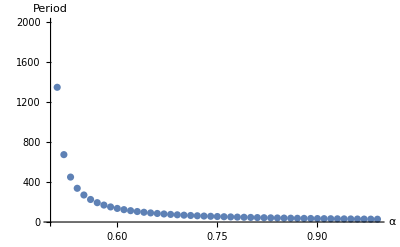

```mathematica
ListPlot[LIPeriods,AxesLabel->{"α","Period"}, PlotRange-> {0,2000}]
(*Try using fourier analysis. *)
```

Great! Now we’ll generate our plot:

```mathematica
PIPLIN=ParallelTable[{αr,αm,
(*Establish a Resident Population with arbitrary initial frequencies:*)
sol=NDSolve[System[αr,0,0.3,1,0.5,0.25,0.28,0.24,0],{u,v1,v2,m1},{t,0,30000},Method->{"StiffnessSwitching"},MaxSteps->10^6];
{uans,v1ans,v2ans,m1ans}= {u[t],v1[t],v2[t],m1[t]}  /.Flatten[sol];
data=Table[{t-8000,v1ans},{t,8000,9100,0.1}];
(*Fit NDSolve output to sin function and find the period for the resident population:*)
Parameters =FindFit[data,{a*Sin[b*(t+c)]+d},{a,b,c,d},t, Method->"NMinimize"];
T1=Abs[(2*π/b)/.Parameters[[2]]];
T1,
(*Introduce mutant invaders at each 0.1*T1 of the cycle:*)
SampleInvasion=Table[{st,
{uf, v1f,v2f,m1f}={u[st],v1[st],v2[st],m1[st]}/.Flatten[sol];                   sol2=NDSolve[System[αr,αm,0.3,1,0.5,uf,v1f,v2f,0.05],{u,v1,v2,m1},{t,0,7*T1},Method->{"StiffnessSwitching"},MaxSteps->10^6];
{uans,v1ans,v2ans,m1ans}= {u[t],v1[t],v2[t],m1[t]}  /.Flatten[sol2];

(*Average mutant frequency several Periods after they invade:*)
m1avg=FindAverage[m1ans,4*T1,7*T1];

If[m1avg>0.05,1,0](*If mutant average frequency has increased from its initial low frequency, we deem this a successful invasion*)}
,
{st,8000,8000+T1,0.01*T1}];

(*Determine if on average the mutants successfully Invade:*)
FlattenedSample=Flatten[SampleInvasion];
AvgResult=Mean[Take[FlattenedSample,{2,-1,2}]];
(*This is the average frequency with which the mutant successfully invaded: *)
AvgResult,
(*Finally, this is a bindary definition of successful invasion: *)
If[AvgResult>0.5,1,0]},
{αr,0.51,0.99,0.01},{αm,0.51,0.99,0.01}];
```

```mathematica
Export["LinearInvasionFinal.csv",PIPLIN];
```

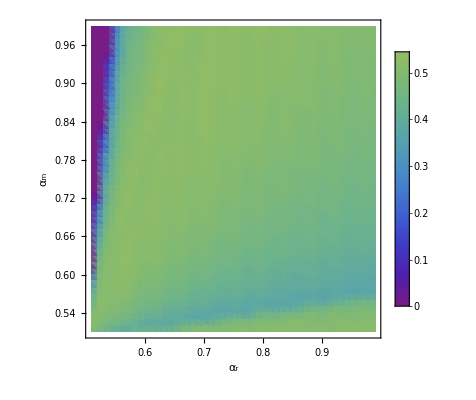

```mathematica
PIPLINF=Flatten[PIPLIN,1];
PlotLIN=PIPLINF[[All,{1,2,4}]];
ListDensityPlot[PlotLIN,PlotLegends->Automatic, ColorFunction->"Rainbow", FrameLabel->{"α_r","α_m"}, ColorFunction->(ColorData["Rainbow"][Rescale[#,{-1,1}]]&),ColorFunctionScaling->False,PlotRange->{-1,1}]
```